# Population annealing analysis

## All trials: N = 64, R = 100, M = 10, K = 100, β = 10, J = 1

N = number of spins
R = initial population size
M = number of MC sweeps per temperature step
K = number of temperature steps
β = target beta
J = J_{ij} matrix seed
C = MC sweep seed
S = initial spin seed
L = randfrom seed

## Import Relevant Files

```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"];
trials=5;
steps=Range[1,100];
energies=Range[1,trials];
pops=Range[1,trials];
For[i=1,i≤trials,i++,
Evaluate[Symbol["energies"<>ToString[i]]]=Import["energies_t"<>ToString[i]<>".csv","CSV"];
energies⟦i⟧=Evaluate[Symbol["energies"<>ToString[i]]];
Evaluate[Symbol["pop"<>ToString[i]]]=Flatten[Import["pop_size_t"<>ToString[i]<>".csv","CSV"]];
pops⟦i⟧=Evaluate[Symbol["pop"<>ToString[i]]];
]
```

## Trial 1: C = 2, S = 3, L = 4

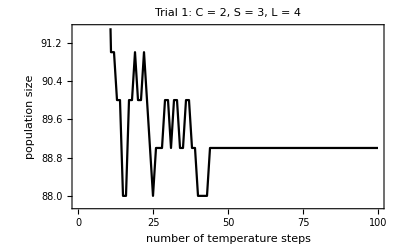

```mathematica
popHist1=ListLinePlot[Transpose[{steps,pops⟦1⟧}],Frame->True,FrameLabel->{"number of temperature steps","population size"},PlotLabel->"Trial 1: C = 2, S = 3, L = 4",LabelStyle->Black,FrameStyle->Black,PlotStyle->Black]
Manipulate[Histogram[energies⟦1⟧⟦sweeps⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 1: C = 2, S = 3, L = 4",LabelStyle->Black,FrameStyle->Black],{sweeps,1,Length[energies⟦1⟧],1}]
```

## Trial 2: C = 3, S = 4, L = 5

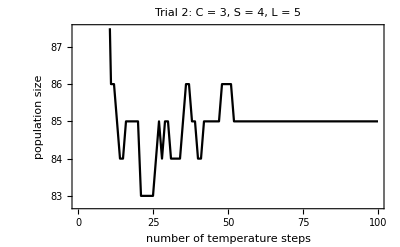

```mathematica
popHist2=ListLinePlot[Transpose[{steps,pops⟦2⟧}],Frame->True,FrameLabel->{"number of temperature steps","population size"},PlotLabel->"Trial 2: C = 3, S = 4, L = 5",LabelStyle->Black,FrameStyle->Black,PlotStyle->Black]
Manipulate[Histogram[energies⟦2⟧⟦sweeps⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 2: C = 3, S = 4, L = 5",LabelStyle->Black,FrameStyle->Black],{sweeps,1,Length[energies⟦2⟧],1}]
```

## Trial 3: C = 4, S = 5, L = 6

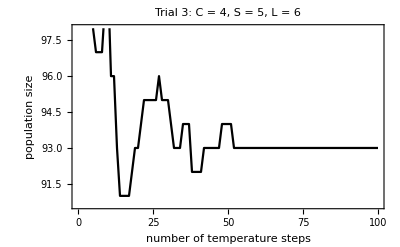

```mathematica
popHist1=ListLinePlot[Transpose[{steps,pops⟦3⟧}],Frame->True,FrameLabel->{"number of temperature steps","population size"},PlotLabel->"Trial 3: C = 4, S = 5, L = 6",LabelStyle->Black,FrameStyle->Black,PlotStyle->Black]
Manipulate[Histogram[energies⟦3⟧⟦sweeps⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 3: C = 4, S = 5, L = 6",LabelStyle->Black,FrameStyle->Black],{sweeps,1,Length[energies⟦3⟧],1}]
```

## Trial 4: C = 5, S = 6, L = 7

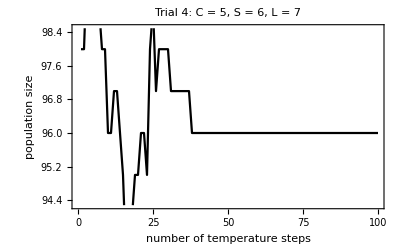

```mathematica
popHist1=ListLinePlot[Transpose[{steps,pops⟦4⟧}],Frame->True,FrameLabel->{"number of temperature steps","population size"},PlotLabel->"Trial 4: C = 5, S = 6, L = 7",LabelStyle->Black,FrameStyle->Black,PlotStyle->Black]
Manipulate[Histogram[energies⟦4⟧⟦sweeps⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 4: C = 5, S = 6, L = 7",LabelStyle->Black,FrameStyle->Black],{sweeps,1,Length[energies⟦4⟧],1}]
```

## Trial 5: C = 6, S = 7, L = 8

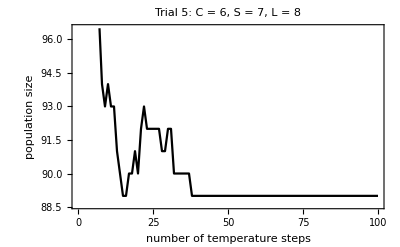

```mathematica
popHist1=ListLinePlot[Transpose[{steps,pops⟦5⟧}],Frame->True,FrameLabel->{"number of temperature steps","population size"},PlotLabel->"Trial 5: C = 6, S = 7, L = 8",LabelStyle->Black,FrameStyle->Black,PlotStyle->Black]
Manipulate[Histogram[energies⟦5⟧⟦sweeps⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 5: C = 6, S = 7, L = 8",LabelStyle->Black,FrameStyle->Black],{sweeps,1,Length[energies⟦5⟧],1}]
```